# Programozási feladat 2.

## Balla Réka N03ZKA

## Konzulens: Karátson János

```mathematica
SetDirectory[NotebookDirectory[]];
```

# Rókák populációdinamikai változásai veszettség hatására

Az elmúlt évtizedekben komoly gondokat okozott Európában a veszettség járvány terjedése  a rókák között. A városok közelében élő rókák veszélyt jelentettek a háziállatokra és emberekre is.A populációdinamikai változásokat leíró modell segítségével vizsgálható, hogy a járvány kialakulásában mely tényezők a meghatározók, és hogyan lehet ezek változtatásával megszüntetni a járványt. 
 A feladatom a modell vizsgálata, a rendszer viselkedésének meghatározása, a paramétertér feltérképezése.

## A modell és az epidemológiai paraméterek

A modell a populáció SEIR osztályozását alkalmazza, ahol S az fogékony, E a kitett, de még nem fertőző, I a fertőző, R pedig a gyógyult egyedek osztálya. Az R osztály az általunk vizsgált modellben már nincs benne, mert a tapasztalatok szerint kevés esély van a természetes gyógyulásra.

Ábra : A veszettség vírus terjedésének alapvető SEIR osztályozása [1]

```mathematica
Image[Import["BallaReka_modell.png"],ImageSize->Large]
```

Az ábrán a rendszer folyamatábrája látható. Az ábrán vázolt populációdinamikát a következő közönséges differenciálegyenlet-rendszer írja le [1]:

S'(t) = r S(t) - γ S(t) N(t) - β S (t) I(t)
E'(t) = β S(t) I(t) - (σ + b + γ N(t)) E(t)
I'(t) = σ E(t) - (α + b + γ N(t)) I(t)
N(t) = S(t) + E(t) + I(t)

Az N(t) az összes egyedszámot jelöli. Az egy főre eső populációnövekedés r = a-b, ahol a az egy főre jutó születési ráta, 1/b pedig az átlagos élettartam. A veszettségnek kitett egyedek száma (E) arányos a fogékony és a fertőző egyedek sűrűségével, ezt fejezi ki β, a betegség terjedésének paramétere. Az átlagos idő, amit egy egyed a kitett osztályban tölt, mielőtt fertőzővé válik, 1/σ. A fertőző egyedek esetében nagyobb a halálozás esélye, a halálozási ráta itt α + b
A születési ráta és az átlag élettartam arányára bevezethetjük a K=a/b egyensúlyi paramétert. A járvány kezdetekor a egyensúlyi egyedszám megegyezik K-val.

Táblázat : Az epidemológiai paraméterek jelentése és alkalmazott értékei [1]

```mathematica
Grid[{{"Szimbólum","Jelentés","Érték"},{"a","Átlagos születései ráta egy főre","1 yr^-1"},{"b","Átlagos természetes halálozási ráta egy főre","0.5 yr^-1"},{"r","Egy főre jutó növekedési ráta, Cell["r=a-b"]","0.5 yr^-1"},{"Κ","Róka eltartóképesség, K=r/γ","Változó, 0 - 20 km^-2"},{"β","Továbbítási tényező Κ_T=1 km^-2 kritikus sűrűség mellett","79.69 km^2/yr"},{"σ","1/σ az átlagos lappangési idő","365/28 yr^-1"},{"α","Veszett rókák halálozási rátája","73 yr^-1"}}]
```

A számításaim során a táblázatban leírt paraméterértékeket használtam.

## Populációdinamika

Anderson [3] szerint a járvány kialakulásának (dI/dt>0) kritériuma az, hogy a vírus reprodukciós rátája nagyobb legyen, mint 1. A modell segítségével megadható reprodukciós ráta (R), és ennek ismeretében a járvány kialakulásához szükséges kritikus sűrűség (Κ_T):

R=K/Κ_T=(K β σ)/((σ+a)(α+a))
Κ_T = ((σ+a)(α+a))/(β σ)

Járvány akkor fog kialakulni, ha R>1  [3]. Ez ekvivalens azzal, hogy az egyensúlyi populációméret meghaladja a kritikus sűrűséget, azaz   Κ>Κ_T. Ekkor a veszettség a betegségmentes egyensúlynál alacsonyabb értéken tartja a populációméretet. Az egyensúlyi álllapot lehet stabilis, ha Κ nem sokkal haladja meg Κ_T értékét, vagy instabilis, ha Κ sokkal nagyobb Κ_T-nél.  Ha R<1 és Κ<Κ_T, akkor a populáció a betegségmentes egyensúlyi állapotba (Κ) rendeződik.

### Adott kezdetiérték-feladatok numerikus megoldása

Az Introductory Differential Equations [2] című könyvben megadott kezdetiértékeket és Κ paramétereket használva megoldottam numerikusan az egyenletrendszert. A megadott értékek:
1. S(0)=0.93,Ε(0)=0.035,Ι(0)=0.035
2.  S(0)=0.93,Ε(0)=0.02,Ι(0)=0.05
Κ={1,2,4,8}

```mathematica
Module[{eqns,pars,init,init2,initsol,init2sol,SEIN,tmax,plotlegends,Kappa,labels,Kappa2},
eqns={S'[t]==(a-b)S[t] - (a-b)/Κ S[t] Ν[t] - β S [t]Ι[t],
Ε'[t]== β S[t]Ι[t]-(σ+b+(a-b)/Κ Ν[t])Ε[t],
Ι'[t]== σ Ε[t] -(α+b+(a-b)/Κ Ν[t])Ι[t],
Ν[t]== S[t]+ Ε[t]+ Ι[t]};
pars={a,b,Κ,β,σ,α};
SEIN={S,Ε,Ι,Ν};
tmax=40;
init={S[0]==0.93,Ε[0]==0.035,Ι[0]==0.035};
initsol=ParametricNDSolve[Flatten[{eqns,init}],SEIN,{t,0,tmax},pars];
init2={S[0]==0.93,Ε[0]==0.02,Ι[0]==0.05};
init2sol=ParametricNDSolve[Flatten[{eqns,init2}],SEIN,{t,0,tmax},pars];
plotlegends={"S(t)","Ε(t)","Ι(t)","Ν(t)"};
labels={"Cell["K=1"]","Cell["K=2"]","Cell["K=8"]"};
Kappa2={1,2,8};
Kappa={1,2,4,8};
Column[
{Style["\nAz S[0]=0.93,Ε[0]=0.035,Ι[0]=0.035 kezdetiértékekhez tartozó megoldások:\n",FontSize->16,FontWeight->"Bold"],
Table[Plot[Evaluate@Table[F[1,0.5,Κ,79.69,365/28,73][t]/.initsol,{F,SEIN}],{t,0,tmax},PlotRange->All,PlotLegends->plotlegends,PlotLabel->"Cell["Κ="]" <>ToString[Κ],AxesLabel->{"Time,t(yr)","Population"}, ImageSize->Medium,LabelStyle->{FontWeight->"Bold",FontSize->12}],{Κ,Kappa}],
Table[Plot[Evaluate@Table[F[1,0.5,Κ,79.69,365/28,73][t]/.initsol,{Κ,Kappa2}],{t,0,tmax},PlotRange->All,PlotLegends->labels,PlotLabel->F[t],ImageSize->Medium,PlotStyle->{ Blue, Red,Green},AxesLabel->{"Time,t(yr)","Population"},LabelStyle->{FontWeight->"Bold",FontSize->12}],{F,SEIN}],
Style["\nAz S[0]=0.93,Ε[0]=0.02,Ι[0]=0.05 kezdetiértékekhez tartozó megoldások:\n",FontSize->16,FontWeight->Bold],
Table[Plot[Evaluate@Table[F[1,0.5,Κ,79.69,365/28,73][t]/.init2sol,{F,SEIN}],{t,0,tmax},PlotRange->All,PlotLegends->plotlegends,PlotLabel->"Cell["Κ="]" <>ToString[Κ],AxesLabel->{"Time, t(yr)","Population"},ImageSize->Medium,LabelStyle->{FontWeight->"Bold",FontSize->12}],{Κ,Kappa}]}]
]
```

A megadott kezdetiértéknél az eredményben nem észleltem szignifikáns különbségeket. A redszer viselkedése az adott paraméterekreaz ábrák alapján nagyon hasonló.  Κ=1 esetén a járvány nem alakul ki. Az egyedszám 10 éven belül visszaáll az egyensúlyi állapotba. A számításnál Κ=2 az a legkisebb érték, melyre az egyedszámok periodikus változást mutatnak, és kialakul a járvány. Ekkor a redszer oszcillálása csillapított, 40 év  elteltével visszaáll az egyedszám az egyensúlyi helyzetbe. Κ=8  esetén a vizsgált időtartományban már nem látható csillapítás, a járvány ekkor fennmarad, kb. 2 éves peririódusidővel.

### Dinamikus megjelenítés

A következőkben a  populáció megoszlását ábrázoltam az idő függvényében és fázistérben. Vátoztatható paraméterek a terület eltartóképessége (Κ) és a lappangási idő (1/σ).  Meg lehet vizsgáli a megoldásokat különböző kezdetiérétkekre és időtávokra.

```mathematica
Manipulate[
Module[{initsol=ParametricNDSolve[
{S'[t]==(a-b)S[t] - (a-b)/Κ S[t] Ν[t] - β S [t]Ι[t],
Ε'[t]== β S[t]Ι[t]-(365/σReciprocalInDays+b+(a-b)/Κ Ν[t])Ε[t],
Ι'[t]== 365/σReciprocalInDays Ε[t] -(α+b+(a-b)/Κ Ν[t])Ι[t],
Ν[t]== S[t]+ Ε[t]+ Ι[t], S[0]==init1,Ε[0]==init2,Ι[0]==init3}
/.{a->1,b->0.5,β->79.69,α->73},{S,Ε,Ι,Ν},{t,0,tmax},{Κ,σReciprocalInDays}]},
{Plot[
Evaluate[{S[Κp,σReciprocalInDaysp][t],Ε[Κp,σReciprocalInDaysp][t],Ι[Κp,σReciprocalInDaysp][t], Ν[Κp,σReciprocalInDaysp][t]}/.initsol],
{t,0,tmax},PlotRange->{0,1.35}, PlotLegends->{S[t],Ε[t],Ι[t],Ν[t]},ImageSize->Large, AxesLabel->{"Time,t(yr)","Population"},PlotStyle->{Blue, Orange, Magenta, Green},AspectRatio->1,LabelStyle->{FontWeight->"Bold",FontSize->12}],
ParametricPlot3D[
Evaluate[{S[Κp,σReciprocalInDaysp][t],Ε[Κp,σReciprocalInDaysp][t],Ι[Κp,σReciprocalInDaysp][t]}/.initsol],
{t,0,tmax},PlotRange->{{0.6,1.35},{0,0.13},{0,0.05}},ImageSize->Large,ColorFunction->"BlueGreenYellow",BoxRatios ->{2,2,1/2},AxesLabel->{S[t],Ε[t],Ι[t]}]}],
{{init1, 0.93,"S(0)"},0.9,1},{{init2, 0.035,"Ε(0)"},0,0.1},{{init3, 0.035,"Ι(0)"},0,0.1},
{{tmax,40,"t_max"},1,200},
{{Κp,2,"fox carrying capacity"},0.25,20},
{{σReciprocalInDaysp,28,"latent period"},1,50},
ControlPlacement->Left,LabelStyle->{FontWeight->"Bold",FontSize->14}
]
```

### Paramétertér ábrázolása

Végül ábrázoltam a rendszer viselkedését a Κ-1/σ paramétertérben. Ez némileg hosszabb számítást igényelt (~15 min), ezért nem töröltem ki az eredményt.

```mathematica
ExtremumQlist[list_]:=Prepend[Append[ Table[{list⟦i⟧,(list⟦i⟧<list⟦i+1⟧ && list⟦i⟧<list⟦i-1⟧)||(list⟦i⟧>list⟦i+1⟧ && list⟦i⟧>list⟦i-1⟧)},{i,2,Length[list]-1}],{list⟦-1⟧,False}],{list⟦1⟧,False}];
Extremums[list_]:=Map[#⟦1⟧&,Select[ExtremumQlist[list],#⟦2⟧==True&]];
OscillationQ[list_]:=Length[Extremums[list]]>5;
DampedOscillationQ[list_]:=If[OscillationQ[list],4/5 Abs[Extremums[list]⟦1⟧-Extremums[list]⟦2⟧]>Abs[Extremums[list]⟦-1⟧-Extremums[list]⟦-2⟧],False];
```

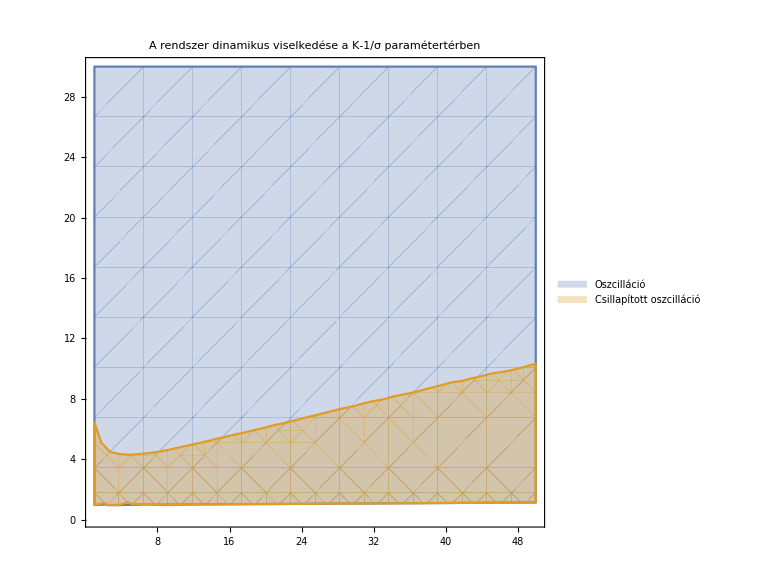

```mathematica
Module[{tmax=40,init1= 0.93,init2= 0.035,init3= 0.035,initsol},
initsol=ParametricNDSolve[
{S'[t]==(a-b)S[t] - (a-b)/Κ S[t] Ν[t] - β S [t]Ι[t],
Ε'[t]== β S[t]Ι[t]-(365/σReciprocalInDays+b+(a-b)/Κ Ν[t])Ε[t],
Ι'[t]== 365/σReciprocalInDays Ε[t] -(α+b+(a-b)/Κ Ν[t])Ι[t],
Ν[t]== S[t]+ Ε[t]+ Ι[t], S[0]==init1,Ε[0]==init2,Ι[0]==init3}
/.{a->1,b->0.5,β->79.69,α->73},{S,Ε,Ι,Ν},{t,0,tmax},{Κ,σReciprocalInDays}];
Off[InterpolatingFunction::dmval];
RegionPlot[{OscillationQ[Evaluate/@Table[Ν[Κ,σReciprocalInDays][t]/.initsol,{t,0,tmax,0.1}]],
DampedOscillationQ[Evaluate/@Table[Ν[Κ,σReciprocalInDays][t]/.initsol,{t,0,tmax,0.1}]]},
{σReciprocalInDays,1,50},{Κ,0.1,30},
PlotPoints->10,PlotLegends->{Style["Oszcilláció",FontWeight->Bold,FontSize->14],Style["Csillapított oszcilláció",FontWeight->Bold,FontSize->14]},PlotLabel->Style["A rendszer dinamikus viselkedése a Κ-1/σ paramétertérben",FontWeight->Bold,FontSize->16],ImageSize->Large]
]
```

Leolvasható, hogy Κ<1 értékekre nem oszcillál a rendszer, nem alakul ki járvány.

Összehasonlításképp Anderson [3] ábrája ugyanerről:

```mathematica
Image[Import["BallaReka_parameterter.png"],ImageSize->Large]
```

Az utóbbi ábrán ciklikus tartományba berajzolt görbék a periódusokat jeölik. A két ábra különbségei a numerikus számításokból adódhatnak.

## Összefoglalás

A járvány elleni védekezésre megoldást jelenthet a populáció méretének kritikus sűrűség alatt tartása (pl.: vadászattal), vakcinázás (az oltóanyag ehető csalétekbe helyezésével), illetve ezek kombinációja. Az immunizálás  hatékonyabb a veszettséggel szemben, azonban következményként az immunissá vált rókák elszaporodása komoly gazdasági és természeti károkat okozhat. A vakcinázás nélkülözése ellen szóló érv, hogy a veszettség más melegvérű állatokra és az emberre is halálos veszélyt jelent, így nem célszerű fenntartani ökológiai szabélyozóként. Az optimális eljárás tehát az immunizálás kombinálása a folyamatos egyedszám szabályozással.

## Irodalomjegyzék

[1]

```mathematica
Hyperlink["Mathematical Models for Rabies - Vijay G. Panjeti, Leslie A. Real","http://origem.info/FIC/pdf/Panjeti_math_models_rabies_Adv_Virus_Res_2011.pdf"]
```

[2]

```mathematica
Hyperlink["Introductory Differential Equations","https://books.google.hu/books?id=3rJZAwAAQBAJ&pg=PA359&lpg=PA359&dq=rabies+in+foxes+differential+equation&source=bl&ots=dB7BLsqTEV&sig=UnYOKLRxqLTP7dsABEIyPd5yH8w&hl=hu&sa=X&ved=0CCwQ6AEwAmoVChMI6aKQq4LyyAIVo55yCh0l-gFM#v=onepage&q=rabies%20in%20foxes%20differential%20equation&f=true"]
```

[3]

```mathematica
Hyperlink["Anderson, R. M., Jackson, H. C., May, R. M., and Smith, A. (1981). Population dynamics of
fox rabies in Europe. Nature 289:765–771.","https://www.researchgate.net/publication/15734042_Population_Dynamics_of_Fox_Rabies_in_Europe"]
```